## RNN Sequence 10

```mathematica
loadTimeSeriesResampled=Import["C:\\Users\\kylem\\Documents\\GitHub\\2019-WSS\\Final Project\\Drafts\\kyle\\LoadtimeseriesResampled.wxf"];
```

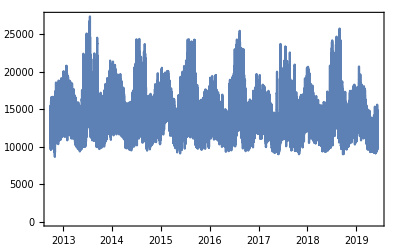

```mathematica
DateListPlot[loadTimeSeriesResampled]
```

```mathematica
data=loadTimeSeriesResampled//Normal;
```

```mathematica
values=QuantityMagnitude@data[[All,2]];keysp=Partition[values,20,1];valuesp = values[[21;;]];
```

```mathematica
threaddata=Thread[Table[ArrayReshape[keysp[[i]],{1,20}]->valuesp[[i]],{i,1,Length@valuesp}]];
```

```mathematica
Length@data
```

58680

```mathematica
Length@threaddata
```

58660

```mathematica
{trainingdata,testdata}=TakeDrop[threaddata,45000];
```

```mathematica
rnn=NetChain[{GatedRecurrentLayer[32,"Dropout"->{"VariationalInput"->0.3},"Input"->{"Varying",20}],GatedRecurrentLayer[64,"Dropout"->{"VariationalInput"->0.3}],GatedRecurrentLayer[64,"Dropout"->{"VariationalInput"->0.3}],SequenceLastLayer[],LinearLayer[128],Ramp,LinearLayer[1]},"Output"->"Scalar"]
```

NetChain[<>]

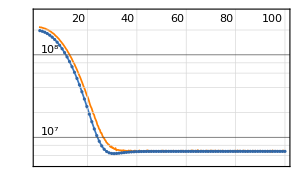
NetTrain Results
summary | ,,  batches:5700  rounds:100  time:6.0min  examples/s:12595
data | ,,  training examples:45000  validation examples:13660  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:6.81×10^6
validation | ,,  loss:6.75×10^6
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set |

```mathematica
trainednet =  NetTrain[rnn,trainingdata,All,ValidationSet->testdata,BatchSize->800,Method-> "ADAM",MaxTrainingRounds->100]
```

```mathematica
AssociationMap[ PredictorMeasurements[
Predict[trainingdata,Method->#,PerformanceGoal->"DirectTraining"],testdata, "MeanSquare"]&,{"RandomForest"}]
```

<|RandomForest→349073.|>

```mathematica
SeedRandom[111];rsample=RandomSample[testdata,2]
```

{{{15571.1,15650.6,15550.,15302.7,15084.7,15006.5,15040.4,15374.6,15861.4,16102.7,16253.8,15728.2,14725.2,13468.8,12628.2,12192.5,11892.3,11734.9,11756.3,11787.6}}→12538.3,{{11153.3,10788.,10716.,10766.8,11116.3,11535.6,12580.1,13398.4,13455.7,13345.3,13460.6,13397.,13189.5,13481.2,13331.1,13720.7,14221.4,14236.6,14295.1,14583.4}}→14470.4}

```mathematica
trainednet[rsample[[2,1]]]
```

NetTrain Results
summary | ,,  batches:5700  rounds:100  time:6.0min  examples/s:12595
data | ,,  training examples:45000  validation examples:13660  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:6.81×10^6
validation | ,,  loss:6.75×10^6
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{{11153.3,10788.,10716.,10766.8,11116.3,11535.6,12580.1,13398.4,13455.7,13345.3,13460.6,13397.,13189.5,13481.2,13331.1,13720.7,14221.4,14236.6,14295.1,14583.4}}]

```mathematica
sobj=NetStateObject[trainednet]
```

NetStateObject::arg1: First argument to NetStateObject should be a valid net.

$Failed

```mathematica
results=Union@Flatten@NestList[Drop[Join[#,{trainedNet[#]}],1]&,testdata[[1,1]],100]
```

{11828.,119}
 |  |  |  |

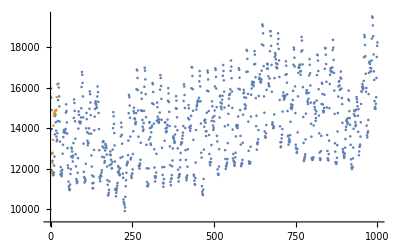

```mathematica
ListPlot[{testdata[[1;;1000,2]],results}]
```